## Setup

```mathematica
Get["FunKit`"]
```

in with ___

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 0.1.1
Year: 2025
For more information and a brief introduction to the package, call FInfo[].
To run the testing suite, you can call  FTest[].

The following defines the scalar field theory and the truncation used. Here, the symmetric phase is assumed by setting Field->{} in the truncation. 
Warning: Setting Field->{ϕ} will give the results for the broken phase, but this will also greatly increase the number of terms in the four- and six-point functions, which may take a long time to compute.

```mathematica
fields= <|
"Commuting"-> {ϕ[p]},
"Grassmann"->{}
|>;
truncation=<|
GammaN->{{ϕ,ϕ},{ϕ,ϕ,ϕ,ϕ}},
Propagator->{{ϕ,ϕ}},
Rdot->{{ϕ,ϕ}},
S->{{ϕ,ϕ},{ϕ,ϕ,ϕ,ϕ}},
Field->{}
|>;
setup=<|
"FieldSpace"->fields,
"Truncation"->truncation
|>;
FSetGlobalSetup[setup];
```

If you would like to see what FunKit does underneath, you can set the debug level to values greater than 0. The numbers correspond to the following level of detail:
0: no info
1: basic information what is happening
2: in-depth what steps are being processed
3: the guts of the program
4: nested guts of the program
5: all details
6: information only needed for debugging

```mathematica
SetFunKitDebugLevel[0];
```

```mathematica
|
```

## DSE

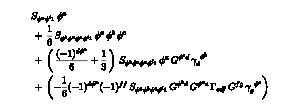

```mathematica
DSE=MakeDSE[ϕ[i1]]//FPrint;
```


-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

```mathematica
DSE2P=FTakeDerivatives[DSE,{ϕ[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

```mathematica
DSE4P=FTakeDerivatives[DSE,{ϕ[i2],ϕ[i3],ϕ[i4]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

```mathematica
DSE6P=FTakeDerivatives[DSE,{ϕ[i2],ϕ[i3],ϕ[i4],ϕ[i5],ϕ[i6]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

## fRG

```mathematica
fRG2P=FTakeDerivatives[WetterichEquation,{ϕ[i1],ϕ[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-

-Graphics-

```mathematica
fRG4P=FTakeDerivatives[WetterichEquation,{ϕ[i1],ϕ[i2],ϕ[i3],ϕ[i4]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-

-Graphics-

```mathematica
fRG6P=FTakeDerivatives[WetterichEquation,{ϕ[i1],ϕ[i2],ϕ[i3],ϕ[i4],ϕ[i5],ϕ[i6]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-

-Graphics-

## 3PI

```mathematica
MakeClassicalAction[setup]+FTerm[-1/2 Log[FTerm[G[{ϕ,ϕ},{i,-i}]]]]+FTerm[S[{ϕ,ϕ},{i,j}],G[{ϕ,ϕ},{-i,-j}]]
```

FEx[FTerm[1/2,S[{ϕ,ϕ},{-i162,-i163}],ϕ[i162],ϕ[i163]],FTerm[1/24,S[{ϕ,ϕ,ϕ,ϕ},{-i164,-i165,-i166,-i167}],ϕ[i164],ϕ[i165],ϕ[i166],ϕ[i167]],FTerm[-1/2 Log[FTerm[G[{ϕ,ϕ},{i,-i}]]]],FTerm[S[{ϕ,ϕ},{i,j}],G[{ϕ,ϕ},{-i,-j}]]]

```mathematica
AddCorrelationFunction[G]
Γ3PI=MakeClassicalAction[setup]+FEx[FTerm[-1/2 Log[FTerm[G[{ϕ,ϕ},{i,-i}]]]]]+FEx[FTerm[S[{ϕ,ϕ},{i,j}],G[{ϕ,ϕ},{-i,-j}]]]
```

FEx[FTerm[-1/2 Log[FTerm[G[{ϕ,ϕ},{i,-i}]]]],FTerm[S[{ϕ,ϕ},{i,j}],G[{ϕ,ϕ},{-i,-j}]],FTerm[1/2,S[{ϕ,ϕ},{-i168,-i169}],ϕ[i168],ϕ[i169]],FTerm[1/24,S[{ϕ,ϕ,ϕ,ϕ},{-i170,-i171,-i172,-i173}],ϕ[i170],ϕ[i171],ϕ[i172],ϕ[i173]]]

```mathematica
FResolveFDOp[setup,FTerm[FDOp[G[{ϕ,ϕ},{g,h}]]]**Γ3PI]
```

in with {}

in with {}

FEx[FTerm[-1/2,FDOp[G[{ϕ,ϕ},{g,h}]],Log[FTerm[G[{ϕ,ϕ},{i,-i}]]]],FTerm[FDOp[G[{ϕ,ϕ},{g,h}]],S[{ϕ,ϕ},{i,j}],G[{ϕ,ϕ},{-i,-j}]],FTerm[1/2,FDOp[G[{ϕ,ϕ},{g,h}]],S[{ϕ,ϕ},{-i168,-i169}],ϕ[i168],ϕ[i169]],FTerm[1/24,FDOp[G[{ϕ,ϕ},{g,h}]],S[{ϕ,ϕ,ϕ,ϕ},{-i170,-i171,-i172,-i173}],ϕ[i170],ϕ[i171],ϕ[i172],ϕ[i173]]][FEx[FTerm[-1/(2 FTerm[G[{ϕ,ϕ},{i20,-i20}]]),FDOp[G[{ϕ,ϕ},{h,g}]],G[{ϕ,ϕ},{i21,-i21}]]],FEx[FTerm[S[{ϕ,ϕ},{h,g}]]],FEx[],FEx[]]

```mathematica
Tuples[{1,5},2]
```

{{1,1},{1,5},{5,1},{5,5}}

```mathematica
SymmetryFactorsFromList[ex_List]:=Module[{ret},
ret=Gather[ex];
ret=1/Factorial[Length[#]]&/@ret;
Times@@ret
];
```

```mathematica
SymmetryFactorsFromList[{ϕ,ϕ,ϕ,q,q,qb,qb}]
```

1/24

```mathematica
AddCorrelationFunction[G]
```

```mathematica
FAddFDRule[G[{f1_,f2_},{i1_,i2_}],G[{df1_,df2_},{di1_,di2_}],γ[{f1,df1},{i1,di1}]γ[{f2,df2},{i2,di2}]]
```

$userRules is now: {{G[{f1_,f2_},{i1_,i2_}],G[{df1_,df2_},{di1_,di2_}],γ[{f1,df1},{i1,di1}] γ[{f2,df2},{i2,di2}]}}

```mathematica
FunKit`Private`FunctionalD[setup,G[{a,b},{c,d}],G[{e,f},{g,h}]]
```

γ[{a,e},{-g,-c}] γ[{b,f},{-h,-d}]

```mathematica
FunKi
```

```mathematica
FunKit`Private`FunctionalD[setup,Log[ϕ[p]],ϕ[i]]
```

FTerm[FDOp[ϕ[i]],Log[ϕ[p]]]

```mathematica
SetFunKitDebugLevel[0]
FTakeDerivatives[setup,FTerm[Log[FTerm[2,ϕ[p],ϕ[-p]]]],{ϕ[i]}]
FTakeDerivatives[setup,%[[1;;1]],{ϕ[j]}]
```

$Aborted

Part::take: Cannot take positions 1 through 1 in $Aborted.

FTakeDerivatives[<|FieldSpace→<|Commuting→{ϕ[p]},Grassmann→{}|>,Truncation→<|GammaN→{{ϕ,ϕ},{ϕ,ϕ,ϕ,ϕ}},Propagator→{{ϕ,ϕ}},Rdot→{{ϕ,ϕ}},S→{{ϕ,ϕ},{ϕ,ϕ,ϕ,ϕ}},Field→{}|>|>,$Aborted⟦1;;1⟧,{ϕ[j]}]

```mathematica
(2 ϕ[-j])/FTerm[2 ϕ[-p19391] ϕ[p19391]]//FullForm
```

Times[2,Power[FTerm[Times[2,\[Phi][Times[-1,p19391]],\[Phi][p19391]]],-1],\[Phi][Times[-1,j]]]

```mathematica
(2 ϕ[-j])/FTerm[2 ϕ[-p19391] ϕ[p19391]]/.Divide[a_,b_]:>a^b
```

2^FTerm[2 ϕ[-p19391] ϕ[p19391]] ϕ[-j]^FTerm[2 ϕ[-p19391] ϕ[p19391]]

```mathematica
Block[{Print},Get["FunKit`"]];
SetFunKitDebugLevel[6]
FunKit`Private`FunctionalD[setup,Log[FTerm[2 ϕ[-p19391] ϕ[p19391]]],ϕ[f]]
FResolveFDOp[setup,%]
```

FunKit 3              Taking functional derivative of Log[FTerm[2 ϕ[-p19391] ϕ[p19391]]] w.r.t. {ϕ[f]}

FunKit 6                          NestRule: Log

FTerm[2,1/FTerm[2 ϕ[-p19391] ϕ[p19391]],FDOp[ϕ[f]],ϕ[-p19391] ϕ[p19391]]

FunKit 2          Found derivative operator FDOp[ϕ[f]] at position 3 in given term.

FunKit 3              Taking functional derivative of ϕ[-p19391] ϕ[p19391] w.r.t. {ϕ[f]}

FunKit 5                      Performed derivative on term 1: FEx[FTerm[2,1/FTerm[2 ϕ[-p19391] ϕ[p19391]],γ[{ϕ,ϕ},{-f,p19391}] ϕ[-p19391]],FTerm[2,1/FTerm[2 ϕ[-p19391] ϕ[p19391]],γ[{ϕ,ϕ},{-f,-p19391}] ϕ[p19391]]]

FunKit 6                          Result: {FEx[FTerm[2,1/FTerm[2 ϕ[-p19391] ϕ[p19391]],γ[{ϕ,ϕ},{-f,p19391}] ϕ[-p19391]],FTerm[2,1/FTerm[2 ϕ[-p19391] ϕ[p19391]],γ[{ϕ,ϕ},{-f,-p19391}] ϕ[p19391]]]}

FunKit 5                      Found factors in FTerm: {γ[{ϕ,ϕ},{-f,p19391}]}

FunKit 5                      Closed indices: {{False,True}}

FunKit 5                      Found factors in FTerm: {γ[{ϕ,ϕ},{-f,-p19391}]}

FunKit 5                      Closed indices: {{False,True}}

FEx[FTerm[(2 ϕ[-f])/FTerm[2 ϕ[-f22407] ϕ[f22407]]],FTerm[(2 ϕ[-f])/FTerm[2 ϕ[-f22408] ϕ[f22408]]]]

```mathematica
(2 ϕ[-j])/FTerm[2 ϕ[-p19391] ϕ[p19391]]//FullForm
```

Times[2,Power[FTerm[Times[2,\[Phi][Times[-1,p19391]],\[Phi][p19391]]],-1],\[Phi][Times[-1,j]]]

```mathematica
FTerm[Sequence[a,b,c]]
```

FTerm[a,b,c]

```mathematica
ReplacePart
```

```mathematica
SetFunKitDebugLevel[0]
FunKit`Private`FunctionalD[setup,2/FTerm[2 ϕ[i]],ϕ[ii]]
SetFunKitDebugLevel[123]
(%%)/2//FResolveFDOp
```

2 FTerm[-2,1/FTerm[2 ϕ[i]]^2,FDOp[ϕ[ii]],ϕ[i]]

FunKit 2          Found derivative operator FDOp[ϕ[ii]] at position 3 in given term.

FunKit 5                      Performed derivative on term 1: FTerm[-2,1/FTerm[2 ϕ[i]]^2,γ[{ϕ,ϕ},{-ii,i}]]

FunKit 6                          Result: {FTerm[-2,1/FTerm[2 ϕ[i]]^2,γ[{ϕ,ϕ},{-ii,i}]]}

FunKit 5                      Found factors in FTerm: {γ[{ϕ,ϕ},{-ii,i}]}

FunKit 5                      Closed indices: {{False,False}}

FEx[FTerm[-2/FTerm[2 ϕ[ii]]^2]]